(1 | Sin[π/9]
2 | Sin[(2 π)/9]
3 | (√3)/2
4 | Cos[π/18]
5 | Cos[π/18]
6 | (√3)/2
7 | Sin[(2 π)/9]
8 | Sin[π/9])

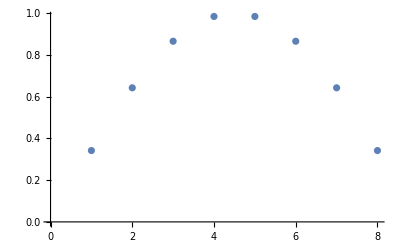

```mathematica
Nsites=8;
n=2;
k=Pi/(Nsites+1);
wavefunction=Table[{j,Sin[k j]},{j,1,Nsites}]; (*matrix do hamiltoniano*)
% // MatrixForm
ListPlot[wavefunction]
```

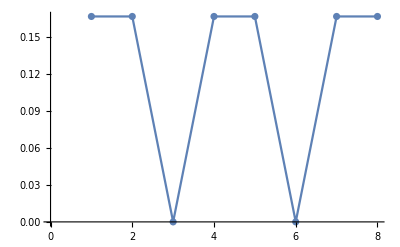

1.

```mathematica
Nsites= 8;
n=6;
k=n Pi/(Nsites+1);
wavefunctionsquare=Table[(2/(Nsites+1)) (Sin[k j])^2,{j,1,Nsites}];
ListPlot[wavefunctionsquare,Joined->True, Mesh->All]
Total[1. wavefunctionsquare]
```